## Import data

```mathematica
(*Open file selector dialog*)
fileDialogResult=SystemDialogInput["FileOpen","*.csv"];
data=Import[fileDialogResult,"CSV","SkipLines"->1];
data=Select[data,Length[#]==4&];(*Remove lines without appropriate data*)
```

## Extract data, set sample rate

```mathematica
fs=250;(*SampleRate of the Pico device*)
(*Get timestamps in seconds*)
(* timestepDiv=1000000000;(*Timestamps since 1970 are encoded as nanoseconds - so we need to divide*)*)
timestepDiv=1000;(*Ticks since reboot in milliseconds - so we need to divide*)
tims=(data[[All,1]]-data[[1,1]])/timestepDiv;(*Take the first column and set the first sample at time zero*)
tims=MedianFilter[tims,3];(*Rarely the Pico throws in an errant timestamp value. This filters outliers*)

(*Extract x,y,z data and substract the mean for each*)
{x,y,z}=Transpose[data[[All,2;;4]]];
x=#-Mean[x]&/@x;
y=#-Mean[y]&/@y;
z=#-Mean[z]&/@z;
```

## Resample the data and plot

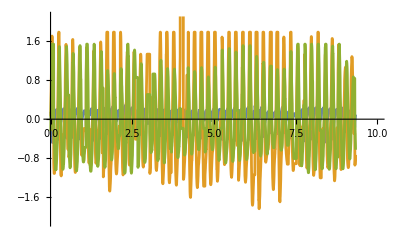

```mathematica
(*Resample data*)
Xdata=TimeSeriesResample[Transpose[{tims,x}],1/fs];(*Forward direction Blue*)
Ydata=TimeSeriesResample[Transpose[{tims,y}],1/fs];(*Side direction Orange*)
Zdata=TimeSeriesResample[Transpose[{tims,z}],1/fs];(*Planar direction Green*)
ListLinePlot[{Xdata,Ydata,Zdata},PlotRange->{{0,10},{-2.1,2.1}}]
```

## Highpass filter

```mathematica
hipass=0.1;
```

```mathematica
x=LowpassFilter[x,2 π hipass/fs];
y=LowpassFilter[y,2 π hipass/fs];
z=LowpassFilter[z,2 π hipass/fs];
```

## Lowpass filter the data and plot again

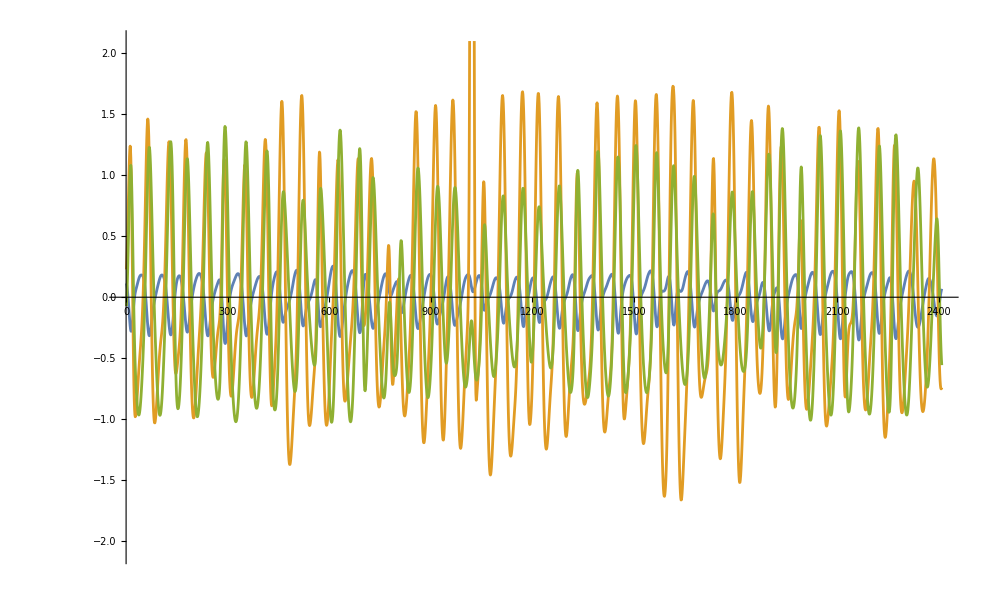

```mathematica
cutoffreq=10;
filtX=LowpassFilter[x,2 π cutoffreq/fs];
filtY=LowpassFilter[y,2 π cutoffreq/fs];
filtZ=LowpassFilter[z,2 π cutoffreq/fs];

ListLinePlot[{filtX,filtY,filtZ},PlotRange->{Automatic,{-2.1, 2.1}}]
```

## Calculate FFTs and plot Periodogram

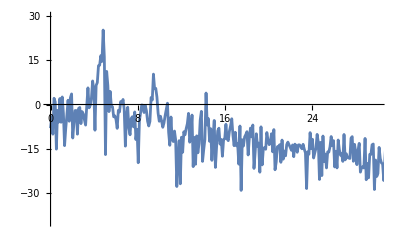

```mathematica
fftX=Abs[Fourier[Xdata[[All,2]]]];
fftY=Abs[Fourier[Ydata[[All,2]]]];
fftZ=Abs[Fourier[Zdata[[All,2]]]];

Periodogram[Zdata[[All,2]],SampleRate->fs,PlotRange->{{0,30},{-40,30}}]
```

## Plot Fourier transform on linear scale

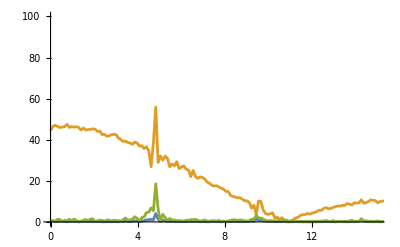

```mathematica
(*x=Range[1/fs,fs/2,fs/Floor[Length[fftX]/2]];*)
plotdataX=fftX[[1;;Floor[Length[fftX]/2]+1]];
plotdataY=fftY[[1;;Floor[Length[fftY]/2]+1]];
plotdataZ=fftZ[[1;;Floor[Length[fftZ]/2]+1]];
fftFreqs=N@Subdivide[1/fs,fs/2,Floor[Length[fftZ]/2]];
ListLinePlot[{Transpose[{fftFreqs,plotdataX}],Transpose[{fftFreqs,plotdataY}],Transpose[{fftFreqs,plotdataZ}]},PlotRange->{{0,cutoffreq*1.5},{0,100}}]
```

## Calculate and plot the zero crossing data

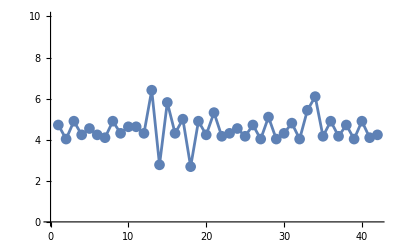

```mathematica
positiveZeroCrossings=Flatten@Position[Differences[Sign[filtZ]],2];

(*Calculate the number of samples between consecutive positive zero crossings*)
samplesBetweenPositiveZeroCrossings=Differences[positiveZeroCrossings];
ListLinePlot[1/(samplesBetweenPositiveZeroCrossings/fs),PlotMarkers->Automatic,PlotRange->{Automatic,{0,cutoffreq}}]
```